# Limit cycles in mass-conserving deficiency-one mass-action systems

Balázs Boros, Josef Hofbauer

This Mathematica Notebook is a supplementary material to the paper which has  the same title as this document.
It contains some of the calculations appearing in the paper.

## 0 Focal values

Derive , and , the first, the second, and the third focal values for the differential equation

Theoretical background: Chapter 4 in Dumortier, Llibre, Artés: Qualitative Theory of Planar Differential Systems.

```mathematica
m = 3;
cd = {}; R2cd = {};
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cd=Join[cd,{Subscript[c, k,i],Subscript[d, k,i]}], R2cd = Join[R2cd,{Subscript[R, k,i]->Subscript[c, k,i]+Subscript[d, k,i] I}]}]];
coeffsxy = CoefficientList[ComplexExpand[Sum[Sum[Subscript[R, k,i] z^(k-i)(z*)^i,{i,0,k}], {k,2,2m+1}]
    /.R2cd/.{z->x+y I}], {x,y}];
cond = True;
For[k=2, k≤2m+1, k++, For[i=0, i≤k, i++,
    {cond = cond && (Subscript[f, i,k-i]==ComplexExpand[Re[coeffsxy[[i+1,k-i+1]]]]) &&
    (Subscript[g, i,k-i]==ComplexExpand[Im[coeffsxy[[i+1,k-i+1]]]])}]];
cd2fg = Solve[cond,cd][[1]];

For[k=2, k≤2m+1, k++, Subscript[R, k]=Sum[Subscript[R, k,i] z^(k-i)w^i,{i,0,k}]];

(* F[i,j] computes the polynomial Subscript[F, i](Subscript[h, j]) *)
F[i_,j_] := Module[{coeffs,M,mtx},
coeffs = CoefficientList[D[Subscript[R, i] Subscript[h, j],{z,1}],{z,w}];
M = Dimensions[coeffs][[1]]-1;
mtx = (coeffs + Transpose[coeffs*]) Table[If[k+l==M&&k≠l,1/(k-l),0],{k,0,M},{l,0,M}];
I (z^Range[0,M]).mtx.w^Range[0,M]];

Subscript[h, 0] = 1;
For[k=1, k≤2m-1, k++, Subscript[h, k] = Sum[F[k+1-l,l],{l,0,k-1}]];

(* H[k,j] computes Subscript[H, k](Subscript[h, j]), note that one of k and j is even, the other one is odd in all of the interesting cases *)
H[k_,j_] := Module[{},
coeffs = CoefficientList[Subscript[h, j],{z,w}];
Sum[Coefficient[Subscript[R, k],z^a w^(k-a)]coeffs[[((k-2a+1)+j)/2+1,(j-(k-2a+1))/2+1]],{a,(k+1-j)/2,(k+1+j)/2}]];
For[j=1,j≤m,j++,Subscript[L, j]=Simplify[ComplexExpand[2π Re[Sum[H[2j+1-l,l],{l,0,2j-1}]]/.R2cd/.cd2fg]]];
```

Display the first focal value, . The second focal value, , is somewhat longer. The third focal value, , is very long. Important note: here  and  include the division by , so they are the Taylor coefficients (not simply the respective derivatives).

```mathematica
Print[" ",Subscript[L, 1]];
```

1/4 π (f_(1,2)+f_(1,1) f_(2,0)+3 f_(3,0)+f_(0,2) (f_(1,1)+2 g_(0,2))+3 g_(0,3)-g_(0,2) g_(1,1)-2 f_(2,0) g_(2,0)-g_(1,1) g_(2,0)+g_(2,1))

Good practice: compute the focal values once, and save them in a file. When needed, load from that file.

```mathematica
L1 = Subscript[L, 1]; L2 = Subscript[L, 2];  L3 = Subscript[L, 3];(* when storing in a file, better avoiding subscripts *)
path="C://bboros/Dropbox/dfc1thm/3d/parallelogram_paper/mathematica/focal_values.mx";
DumpSave[path,{L1,L2,L3}];
Protect[path];
Off[Remove::rmptc];
Remove["Global`*"]; (* clear all variables *)
On[Remove::rmptc];
Unprotect[path];
```

Define a module that computes the necessary partial derivatives. To be used later.

```mathematica
GetDerivatives[fg_,equilibrium_,m_]:=Module[{J,xyshift,T,Tinvuv,FG,derivatives,a,b,u,v},
J=Simplify[D[fg,{{x,y}}]/.equilibrium];
xyshift = {x->x+(x/.equilibrium), y->y+(y/.equilibrium)};
T = {{1,0},{-a/ω,-b/ω}};
Tinvuv = Inverse[T].{u,v};
FG = (T . fg/.xyshift)/ω /.{x->Tinvuv[[1]],y->Tinvuv[[2]]}/.{a->J[[1,1]],b-> J[[1,2]]};
derivatives={};
For[i=0, i≤2m+1, i++, For[j=0, j≤2m+1-i, j++, 
derivatives = Join[derivatives, {Subscript[f, i,j]->(D[FG[[1]],{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0}), Subscript[g, i,j]->(D[FG[[2]],{u,i},{v,j}]/((i!)*( j!))/.{u->0,v->0})}]]];
derivatives];
```

## 3 Parallelograms

### 3.1 Supercritical Andronov-Hopf bifurcation

Start with the planar parallelogram () and compute the first focal value. Observe that it is negative. Thus, the Andronov-Hopf bifurcation is supercritical, and a stable limit cycle is born.

```mathematica
κpositive=Subscript[κ, 1]>0&&Subscript[κ, 2]>0&&Subscript[κ, 3]>0&&Subscript[κ, 4]>0;
fg=Subscript[κ, 1] y {1,-1}+Subscript[κ, 2] x {0,2}+Subscript[κ, 3] x y^2{-1,1}+Subscript[κ, 4] y^3{0,-2};
equilibrium={x->((Subscript[κ, 1]^3 Subscript[κ, 4])/(Subscript[κ, 3]^3 Subscript[κ, 2]))^(1/4),y->((Subscript[κ, 1] Subscript[κ, 2])/(Subscript[κ, 3] Subscript[κ, 4]))^(1/4)};
J=D[fg,{{x,y}}]/.equilibrium;
trJ=Simplify[Tr[J],κpositive];
tracevanish=Normal[Solve[trJ==0&&κpositive][[1]]];
ωsubst = Simplify[{ω->√Det[J]},κpositive];
derivatives=Simplify[GetDerivatives[fg,equilibrium,1],κpositive];
Get[path];
Print[" ",Simplify[L1/.derivatives/.ωsubst/.tracevanish,κpositive]];
```

-(π (κ_3 κ_4)^(3/2))/(√2 κ_2 (κ_3+6 κ_4)^2)

Let us now lift the planar parallelogram by adding a new species in a way that rank of the network remains two (in fact, the Euclidean embedded graph remains a parallelogram).
Verify that the formula for the equilibria and the trace are correct.

```mathematica
fgh=Subscript[κ, 1] y z^γ{1,-1,0}+Subscript[κ, 2] x z^γ{0,2,-γ}+Subscript[κ, 3] x y^2{-1,1,0}+Subscript[κ, 4] y^3{0,-2,γ};
equilibrium={x->((Subscript[κ, 1] Subscript[κ, 4])/(Subscript[κ, 2] Subscript[κ, 3]))^(1/2)t^γ ,y->t^γ,z->((Subscript[κ, 3] Subscript[κ, 4])/(Subscript[κ, 1] Subscript[κ, 2]))^(1/(2γ))t^2};
trJ=(√((Subscript[κ, 1] Subscript[κ, 3] Subscript[κ, 4])/Subscript[κ, 2])-(Subscript[κ, 3]+6 Subscript[κ, 4]))t^(2γ)-γ^2 Subscript[κ, 4]((Subscript[κ, 1] Subscript[κ, 2])/(Subscript[κ, 3] Subscript[κ, 4]))^(1/(2γ))t^(3γ-2);
J=D[fgh,{{x,y,z}}];
Print["the equilibria are given correctly: ",Simplify[fgh/.equilibrium,κpositive&&t>0&&γ>0]=={0,0,0}];
Print["the trace is given correctly: ",Simplify[trJ-Tr[J]/.equilibrium,κpositive&&t>0&&γ>0]==0];
```

the equilibria are given correctly: True

the trace is given correctly: True

We reparametrise the rate constants to make the formulas somewhat lighter.
Then we compute the derivatives that will be plugged in to the focal value formula.

```mathematica
abcdpositive=a>0&&b>0&&c>0&&d>0;
κ2abcd={Subscript[κ, 1]->a^(2γ),Subscript[κ, 2]->b^(2γ),Subscript[κ, 3]->c^(2γ),Subscript[κ, 4]->d^(2γ)};
fg=Simplify[fgh[[1;;2]]/.{z->((γ x+γ y+2z/.equilibrium)-γ x-γ y)/2}];
derivatives=Simplify[GetDerivatives[fg,equilibrium,1]/.κ2abcd,abcdpositive&&t>0&&γ>0];
J=D[fg,{{x,y}}]/.equilibrium/.κ2abcd;
ωsubst=Simplify[{ω->√Det[J]},abcdpositive&&t>0&&γ>0];
```

#### 3.1.1 Case

We take  (when , due to the homogeneity, the dynamics is the same in every stoichiometric class).
It turns out  is negative, and thus, the Andronov-Hopf bifurcation is always supercritical.

```mathematica
γsubst={γ->2};
tsubst={t->1};
dersimple=Simplify[derivatives/.γsubst/.tsubst];
trJsimple=Simplify[trJ/.κ2abcd/.γsubst/.tsubst,abcdpositive];
ωsimple=Simplify[ωsubst/.γsubst/.tsubst,abcdpositive];
L1abcd=Simplify[L1/.dersimple];
L1enum=Simplify[ω^3 L1abcd/.ωsimple];(* the multiplication by  is to simplify the formula a bit *)
Print[" is nonnegative for: ",Reduce[L1enum>=0&&trJsimple==0&&abcdpositive]];
Print[" is negative for: ",Reduce[L1enum<0&&trJsimple==0&&abcdpositive]];
Print["the trace vanishes for: ",Reduce[trJsimple==0&&abcdpositive]];
```

is nonnegative for: False

is negative for: d>0&&c>0&&b>0&&a==(2 b^3 d)/c^3+√((b^2 c^8+4 b^6 d^4+6 b^2 c^4 d^4)/(c^6 d^2))

the trace vanishes for: d>0&&c>0&&b>0&&a==(2 b^3 d)/c^3+√((b^2 c^8+4 b^6 d^4+6 b^2 c^4 d^4)/(c^6 d^2))

#### 3.1.2 Case

Below we compute and analyse and the first focal value for fixed values of . We find that it is negative.
Notice that we do another reparametrisation for convenience.
Further, the analysis of the sign of the first focal value is performed by investigating the enumerator and the denominator separately (this seems to be a lot faster).

```mathematica
gammas={1,3,4,5,6};
For[i=1,i<=Length[gammas],i++,{
gamma=gammas[[i]];
Print[Style[StringJoin["",ToString[gamma]],{Blue,Bold}]];
γsubst={γ->gamma};
tHopf={t->(1/γ^2((a/b)^γ-(c/d)^γ-6(d/c)^γ)(c d)/(a b)(c/d)^γ)^(1/(γ-2))};(* solution of  *)
ωsimple=Simplify[ωsubst/.γsubst,abcdpositive&&t>0];
dersimple=Simplify[derivatives/.γsubst,abcdpositive&&t>0];
tsimple=Simplify[tHopf/.γsubst];
L1simple=Simplify[L1/.dersimple/.ωsimple];
L1abcd=Simplify[L1simple/.tsimple,abcdpositive];
abcd2ABCD={a->A^(1/γ),b->B^(1/γ),c->C^(1/γ),d->D^(1/γ)}/.γsubst;(* another reparametrisation *)
ABCDpositive=A>0&&B>0&&C>0&&D>0;
L1ABCD=Simplify[L1abcd/.abcd2ABCD,ABCDpositive];
condHopf=A/B-C/D-6 D/C>0;(* condition for Hopf *)
L1enum=Numerator[L1ABCD];
L1denom=Denominator[L1ABCD];
Print[" ",L1ABCD];
If[gamma>2,{
Print["enumerator of  is positive for ",Reduce[L1enum>0&&ABCDpositive&&condHopf,A]];
Print["denominator of  is negative for ",Reduce[L1denom<0&&ABCDpositive&&condHopf,A]];
},
{
Print["enumerator of  is negative for ",Reduce[L1enum<0&&ABCDpositive&&condHopf,A]];
Print["denominator of  is positive for ",Reduce[L1denom>0&&ABCDpositive&&condHopf,A]];
}];
}];
```

1

-((√C (A C D-B (C^2+6 D^2))^2 (3 A^6 C^4 D^6-2 A^5 B C^3 D^5 (3 C^2+31 D^2)+A^4 B^2 C^2 D^4 (-C^4+98 C^2 D^2+516 D^4)+8 A^3 B^3 C D^3 (C^6+4 C^4 D^2-65 C^2 D^4-261 D^6)+B^6 C^2 (C^8+18 C^6 D^2+108 C^4 D^4+232 C^2 D^6+96 D^8)+2 A B^5 C D (-C^8+3 C^6 D^2+128 C^4 D^4+620 C^2 D^6+720 D^8)+A^2 B^4 D^2 (-3 C^8-92 C^6 D^2-360 C^4 D^4+648 C^2 D^6+3456 D^8)) π)/(8 √2 A^4 B^4 D^4 (A C D-B (C^2+4 D^2)) (A^2 C D^2-6 A B D^3-B^2 (C^3+2 C D^2))^(3/2)))

enumerator of  is negative for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

denominator of  is positive for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

3

((59049 B^8 D^8 (3 A^6 C^3 D^6-2 A^5 B C^2 D^5 (C^2-9 D^2)-3 A^4 B^2 C D^4 (3 C^4-2 C^2 D^2+180 D^4)+6 A B^5 C^2 D (-C^6+C^4 D^2+28 C^2 D^4+84 D^6)+8 A^3 B^3 D^3 (C^6-2 C^4 D^2-18 C^2 D^4+243 D^6)+A^2 B^4 C D^2 (5 C^6-36 C^4 D^2+384 C^2 D^4+1080 D^6)+B^6 (C^9+22 C^7 D^2+132 C^5 D^4+216 C^3 D^6)) π)/(8 √2 C^(5/2) (B C^2-A C D+6 B D^2)^6 (-A C D+B (C^2+4 D^2)) (A^2 C D^2-6 A B D^3-B^2 (C^3+2 C D^2))^(3/2)))

enumerator of  is positive for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

denominator of  is negative for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

4

((256 √2 B^5 D^5 (3 A^6 C^4 D^6+88 A^5 B C^3 D^7-A^4 B^2 C^2 D^4 (13 C^4+40 C^2 D^2+1464 D^4)+8 A^3 B^3 C D^3 (C^6-14 C^4 D^2-14 C^2 D^4+684 D^6)+A^2 B^4 D^2 (9 C^8+16 C^6 D^2+1344 C^4 D^4+2592 C^2 D^6-3024 D^8)+B^6 C^2 (C^8+24 C^6 D^2+120 C^4 D^4-32 C^2 D^6-624 D^8)-8 A B^5 C D (C^8-3 C^6 D^2-14 C^4 D^4+76 C^2 D^6+360 D^8)) π)/(A C^(5/2) (B C^2-A C D+6 B D^2)^4 (-A C D+B (C^2+4 D^2)) (A^2 C D^2-6 A B D^3-B^2 (C^3+2 C D^2))^(3/2)))

enumerator of  is positive for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

denominator of  is negative for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

5

((625 5^(2/3) B^4 D^4 (3 A^6 C^4 D^6+2 A^5 B C^3 D^5 (C^2+89 D^2)-A^4 B^2 C^2 D^4 (17 C^4+86 C^2 D^2+2652 D^4)+8 A^3 B^3 C D^3 (C^6-32 C^4 D^2-23 C^2 D^4+1251 D^6)+A^2 B^4 D^2 (13 C^8+84 C^6 D^2+2696 C^4 D^4+4968 C^2 D^6-6912 D^8)+B^6 C^2 (C^8+26 C^6 D^2+92 C^4 D^4-440 C^2 D^6-1632 D^8)-2 A B^5 C D (5 C^8-27 C^6 D^2-24 C^4 D^4+1108 C^2 D^6+3600 D^8)) π)/(8 √2 A^(4/3) C^(13/6) (-A C D+B (C^2+4 D^2)) (A C D-B (C^2+6 D^2))^(10/3) (A^2 C D^2-6 A B D^3-B^2 (C^3+2 C D^2))^(3/2)))

enumerator of  is positive for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

denominator of  is negative for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

6

((81 √2 B^(5/2) D^(7/2) (3 A^6 C^4 D^6+4 A^5 B C^3 D^5 (C^2+72 D^2)-3 A^4 B^2 C^2 D^4 (7 C^4+44 C^2 D^2+1368 D^4)+8 A^3 B^3 C D^3 (C^6-56 C^4 D^2-45 C^2 D^4+1944 D^6)+A^2 B^4 D^2 (17 C^8+168 C^6 D^2+4440 C^4 D^4+8208 C^2 D^6-11664 D^8)+B^6 C^2 (C^8+28 C^6 D^2+48 C^4 D^4-1008 C^2 D^6-3024 D^8)-12 A B^5 C D (C^8-8 C^6 D^2+2 C^4 D^4+360 C^2 D^6+1080 D^8)) π)/(A^(3/2) C^2 √(-C^3+((A^2-2 B^2) C D^2)/B^2-(6 A D^3)/B) (-A C D+B (C^2+4 D^2)) (-A C D+B (C^2+6 D^2))^3 (-A^2 C D^2+6 A B D^3+B^2 (C^3+2 C D^2))))

enumerator of  is positive for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

denominator of  is negative for C>0&&D>0&&B>0&&A>(B C^2+6 B D^2)/(C D)

### 3.2 Subcritical Andronov-Hopf bifurcation

Start with the planar parallelogram () and compute the first focal value. Observe that it can have any sign. Thus, the Andronov-Hopf bifurcation can be subcritical (unlike for the parallelograms in Section 3.1). Hence, an unstable limit cycle can be born, which is necessarily surrounded by a stable limit cycle (the system is permanent).

```mathematica
fg=Subscript[κ, 1] y {1,-1}+Subscript[κ, 2] x {0,2}+Subscript[κ, 3] x y^2{-1,1}+Subscript[κ, 4] y^3{0,-2}+Subscript[κ, 5] x y^2{0,-2}+Subscript[κ, 6] y{0,2}/.{Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->a,Subscript[κ, 5]->4 a,Subscript[κ, 6]->b,Subscript[κ, 4]->4 b};
equilibrium=Simplify[Solve[fg==0&&a>0&&b>0&&x>0&&y>0][[1]],a>0&&b>0];
J=D[fg,{{x,y}}]/.equilibrium;
trJ=Tr[J];
tracevanish=Solve[trJ==0&&a>0&&b>0,b][[1]];
Print[" for ",tracevanish];
ωsubst = {ω->√Det[J]};
derivatives=Simplify[GetDerivatives[fg,equilibrium,1]];
Get[path];
L1a=Simplify[L1/.derivatives/.ωsubst/.tracevanish];
Print[" ",L1a];
Print[" and  for ",Reduce[L1a>0&&trJ==0&&a>0&&b>0,b]]
```

for {b→ConditionalExpression[1/16 (3-64 a), 0<a<3/64]}

ConditionalExpression[((15-1312 a+15360 a^2) π)/(12 √3), 0<a<3/64]

and  for 0<a<1/960 (41-√781)&&b==1/16 (3-64 a)

Let us now lift the planar parallelogram by adding a new species in a way that rank of the network remains two (in fact, the Euclidean embedded graph remains a parallelogram).
Verify that the formula for the equilibria and the trace are correct.

```mathematica
fgh=Subscript[κ, 1] y z^γ{1,-1,0}+Subscript[κ, 2] x z^γ{0,2,-γ}+Subscript[κ, 3] x y^2{-1,1,0}+Subscript[κ, 4] y^3{0,-2,γ}+Subscript[κ, 5] x y^2{0,-2,γ}+Subscript[κ, 6] y z^γ{0,2,-γ}/.{Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->a,Subscript[κ, 5]->4 a,Subscript[κ, 6]->b,Subscript[κ, 4]->4 b};
equilibrium={x->2 t^γ ,y->1/2 t^γ,z->t^2};
trJ=4 t^(2γ)((3/16-4a-b)-γ^2/8(4a+b)t^(γ-2));
J=D[fgh,{{x,y,z}}];
Print["the equilibria are given correctly: ",Simplify[fgh/.equilibrium,a>0&&b>0&&t>0&&γ>0]=={0,0,0}];
Print["the trace is given correctly: ",Simplify[trJ-Tr[J]/.equilibrium,a>0&&b>0&&t>0&&γ>0]==0];
```

the equilibria are given correctly: True

the trace is given correctly: True

Next, we compute the first focal value.

```mathematica
fg=Simplify[fgh[[1;;2]]/.{z->((γ x+γ y+2z/.equilibrium)-γ x-γ y)/2}];
derivatives=Simplify[GetDerivatives[fg,equilibrium,1],a>0&&b>0&&t>0&&γ>0];
J=D[fg,{{x,y}}]/.equilibrium;
ωsubst=Simplify[{ω->√Det[J]},a>0&&b>0&&t>0&&γ>0];
L1abtγ=Simplify[Simplify[L1/.derivatives]/.ωsubst];
Print[" ",L1abtγ];
```

1/(32 √2 (4 t^2+t^γ γ^2)^3 ((4 a+b) (8 t^2+5 t^γ γ^2))^(3/2))π t^(-3-2 γ) (128 (3+131072 a^3+24 b-1664 b^2+12288 b^3+4096 a^2 (-3+40 b)+320 a (-1-40 b+256 b^2)) t^12+32 (9+950272 a^3+452 b-11936 b^2+89600 b^3+512 a^2 (-209+2416 b)+64 a (-15-1588 b+9504 b^2)) t^(10+γ) γ^2-20 (4 a+b)^2 t^(6 γ) (-1+γ) γ^10 (8 a (-4+γ)+b (-8+7 γ))+4 t^(8+2 γ) γ^3 (-9 (3+γ)+32768 a^3 (2+121 γ)+24 b (-35+124 γ)-320 b^2 (-13+145 γ)+512 b^3 (-2+847 γ)+1024 a^2 (29-526 γ+8 b (2+695 γ))+32 a (-3 (8+15 γ)+64 b^2 (-2+1421 γ)-8 b (-94+1949 γ)))-t^(4+4 γ) γ^6 (4096 a^3 (50-219 γ+179 γ^2)-4 a (81-183 γ-330 γ^2+64 b^2 (-150+781 γ+11 γ^2)+16 b (-117-71 γ+96 γ^2))+b (-81+318 γ+275 γ^2+b (936+736 γ-10632 γ^2)-64 b^2 (-50+281 γ+265 γ^2))+128 a^2 (117+50 γ-163 γ^2+8 b (150-719 γ+433 γ^2)))-2 t^(2+5 γ) γ^8 (512 a^3 (91-205 γ+114 γ^2)+b^2 (9 (3+19 γ-54 γ^2)+8 b (91-270 γ+139 γ^2))+16 a^2 (27+141 γ-146 γ^2+8 b (273-680 γ+417 γ^2))+8 a b (27+156 γ-191 γ^2+4 b (273-745 γ+442 γ^2)))+2 t^(6+3 γ) γ^4 (3 (9-17 γ) γ+12 b γ (-133+101 γ)+32768 a^3 (-2+17 γ+19 γ^2)-16 b^2 (36-335 γ+145 γ^2)+256 b^3 (-4+32 γ+743 γ^2)+256 a^2 (-36+167 γ-737 γ^2+64 b (-3+25 γ+105 γ^2))+8 a (-γ (339+151 γ)+128 b^2 (-12+98 γ+1125 γ^2)-16 b (36-251 γ+1476 γ^2))))

#### 3.2.1 Case

In the  case we set may . Further, we eliminate  using . The first focal value formula then becomes very simple.

ConditionalExpression[1/32 √7 (-7-16 b+1280 b^2) π, 0<b<1/8]

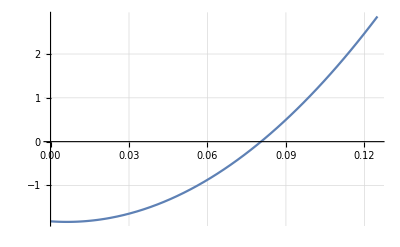

```mathematica
asubst=Solve[(trJ/.{γ->2,t->1})==0&&a>0&&b>0,a][[1]];
L1b=Simplify[L1abtγ/.{γ->2,t->1}/.asubst];
Print[" ",L1b];
Plot[L1b,{b,0,1/8},GridLines->Automatic]
```

#### 3.2.2 Case

Solve  for . Also, define the region in the -plane, which admits an Andronov-Hopf bifurcation.

```mathematica
tsubst={t->((3/16-4 a-b)/(1/8 (4 a+b) γ^2))^(1/(γ-2))};
hopfab=(3/16-4 a-b>0)&&a>0&&b>0;
```

Plot the sign of the first focal value for  and .

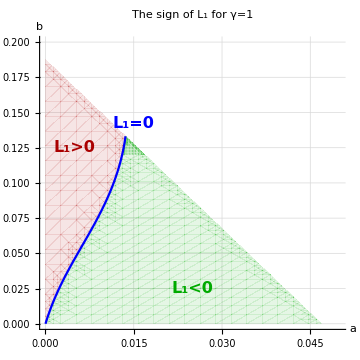
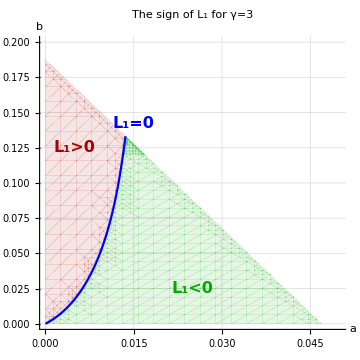

```mathematica
γsubsts={{γ->1},{γ->3}};
toshow={};
For[i=1,i<=Length[γsubsts],i++,{
γsubst=γsubsts[[i]];
L1ab=Simplify[L1abtγ/.tsubst/.γsubst];
L1pos=Reduce[L1ab>0&&hopfab];
L1neg=Reduce[L1ab<0&&hopfab];
L1zero=Solve[L1ab==0&&hopfab,b][[1]];
amax=L1zero[[1]][[2]][[2]][[5]];

rplpos=RegionPlot[L1pos,{a,0,0.05},{b,0,0.2},PlotStyle->{Darker[Red],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[a,Bold,16],Style[b,Bold,16]},Frame->None,Axes->True,PlotLabel->Style[StringJoin["The sign of L_1 for γ=",ToString[γ/.γsubst]],Bold,16],ImageSize->Medium];
rplnega=RegionPlot[L1neg,{a,0,0.05},{b,0,0.12},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None];
rplnegb=RegionPlot[L1neg,{a,0.01,0.02},{b,0.12,0.14},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None];
pl=Plot[b/.L1zero,{a,0,amax},PlotStyle->Blue];
txt=Graphics[{Text[Style["L_1>0",Darker[Red],Bold,16],{0.005,0.125}],
Text[Style["L_1=0",Blue,Bold,16],{0.015,0.142}],
Text[Style["L_1<0",Darker[Green],Bold,16],{0.025,0.025}]}];
toshow=Join[toshow,{Show[rplpos,rplnega,rplnegb,pl,txt]}];
}];
Row[toshow]
```

### 3.3 Two Andronov-Hopf points

Start with the planar parallelogram (set the stoichiometric coefficient of  to zero in every complex) and compute the first focal value. Observe that it can have any sign. Thus, the Andronov-Hopf bifurcation can be subcritical (unlike for the parallelograms in Section 3.1). Hence, an unstable limit cycle can be born, which is necessarily surrounded by a stable limit cycle (the system is permanent).

```mathematica
fg=Subscript[κ, 1] y {2,-1}+Subscript[κ, 2] x^2 {0,2}+Subscript[κ, 3] x^2 y^2{-2,1}+Subscript[κ, 4] y^3{0,-2}+Subscript[κ, 5] x^2 y^2{0,-2}+Subscript[κ, 6] y{0,2}/.{Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->a,Subscript[κ, 5]->16 a,Subscript[κ, 6]->b,Subscript[κ, 4]->16 b};
equilibrium=Simplify[Solve[fg==0&&a>0&&b>0&&x>0&&y>0][[1]],a>0&&b>0];
J=D[fg,{{x,y}}]/.equilibrium;
trJ=Tr[J];
tracevanish=Solve[trJ==0&&a>0&&b>0,b][[1]];
Print[" for ",tracevanish];
ωsubst = {ω->√Det[J]};
derivatives=Simplify[GetDerivatives[fg,equilibrium,1]];
Get[path];
L1a=Simplify[L1/.derivatives/.ωsubst/.tracevanish];
Print[" ",L1a];
Print[" and  for ",Reduce[L1a>0&&trJ==0&&a>0&&b>0,b]]
```

for {b→ConditionalExpression[1/8 (1-128 a), 0<a<1/128]}

ConditionalExpression[(45/32-592 a+36864 a^2) π, 0<a<1/128]

and  for 0<a<(37-√559)/4608&&b==1/8 (1-128 a)

Let us now lift the planar parallelogram by adding a new species in a way that rank of the network remains two (in fact, the Euclidean embedded graph remains a parallelogram).
Verify that the formula for the equilibria and the trace are correct.

```mathematica
fgh=Subscript[κ, 1] y z^γ{2,-1,0}+Subscript[κ, 2] x^2 z^γ{0,2,-γ}+Subscript[κ, 3] x^2 y^2{-2,1,0}+Subscript[κ, 4] y^3{0,-2,γ}+Subscript[κ, 5] x^2 y^2{0,-2,γ}+Subscript[κ, 6] y z^γ{0,2,-γ}/.{γ->1,Subscript[κ, 1]->1,Subscript[κ, 3]->1,Subscript[κ, 2]->a,Subscript[κ, 5]->4 a,Subscript[κ, 6]->b,Subscript[κ, 4]->4 b};
equilibrium={x->t ,y->1/4 t^2,z->1/4 t^4};
trJ=1/4 t^2(-t^3+(1-4(4a+b))t^2-(4a+b));
J=D[fgh,{{x,y,z}}];
Print["the equilibria are given correctly: ",Simplify[fgh/.equilibrium,a>0&&b>0&&t>0&&γ>0]=={0,0,0}];
Print["the trace is given correctly: ",Simplify[trJ-Tr[J]/.equilibrium,a>0&&b>0&&t>0&&γ>0]==0];
```

the equilibria are given correctly: True

the trace is given correctly: True

Next, we find that there are exactly two distinct positive ’s for which the trace vanishes if and only if . The two roots coincide (both of them equal to ) when .
Further, for , one root is smaller than , while the other is larger. The situation is in fact slightly simpler: one root is smaller than , while the other is larger (this is because  for any , see below).

```mathematica
p=-t^3+(1-4c)t^2-c;
Reduce[p==0&&c>0&&t>0,t]
Reduce[D[p,t]==0&&t>0&&c>0,t]
Reduce[Simplify[p/.{t->1/2}]>0&&c<1/16]
```

(0<c<1/16&&(t==Root[c+(-1+4 c) #1^2+#1^3&,2]||t==Root[c+(-1+4 c) #1^2+#1^3&,3]))||(c==1/16&&t==1/2)

0<c<1/4&&t==1/3 (2-8 c)

c<1/16

Next, we compute the first focal value. We eliminate  using , so only two parameters are left:  and .

```mathematica
fg=Simplify[fgh[[1;;2]]/.{z->((x+2y+4z/.equilibrium)- x-2 y)/4}];
derivatives=Simplify[GetDerivatives[fg,equilibrium,2],a>0&&b>0&&t>0];
J=D[fg,{{x,y}}]/.equilibrium;
ωsubst=Simplify[{ω->√Det[J]},a>0&&b>0&&t>0];
L1abt=Simplify[Simplify[L1/.derivatives]/.ωsubst];
Print[" ",L1abt];
```

1/(8 t^5 (1+2 t^2)^2 ((4 a+b) (1+t+4 t^3))^(3/2))π (2048 a^3 t^3 (-1+7 t+6 t^2-6 t^3+48 t^4+8 t^5+64 t^7)-t^5 (8-34 t+36 t^2+t^3-71 t^4+72 t^5-12 t^6-36 t^7+36 t^8)+4 b t^2 (-4+8 t+4 t^2-10 t^3+21 t^4+29 t^5-18 t^6+38 t^7+16 t^8+24 t^9)+16 b^3 (1+t+20 t^2+32 t^3+80 t^4+228 t^5+108 t^6+480 t^7+496 t^8+768 t^10)+8 b^2 (2+t+8 t^2+18 t^3-32 t^4+48 t^5+104 t^6-220 t^7+272 t^8+184 t^9-320 t^10+448 t^11)+32 a^2 t (-4+11 t-29 t^2-80 t^3+28 t^4-20 t^5-372 t^6+240 t^7+128 t^8-512 t^9+448 t^10+8 b (-1+9 t+66 t^3+124 t^4-36 t^5+480 t^6+176 t^7+640 t^9))+8 a (-t^2 (4-8 t+9 t^2+16 t^3+49 t^4+2 t^5+104 t^6+116 t^7-4 t^8+96 t^9+48 t^10)+8 b^2 (1+29 t^2+34 t^3+132 t^4+340 t^5+84 t^6+864 t^7+656 t^8+1280 t^10)+b (4-12 t+7 t^2-81 t^3-376 t^4-140 t^5-372 t^6-1732 t^7+176 t^8-544 t^9-1792 t^10+704 t^11)))

Next, we find and plot the regions with the various sign structures of .

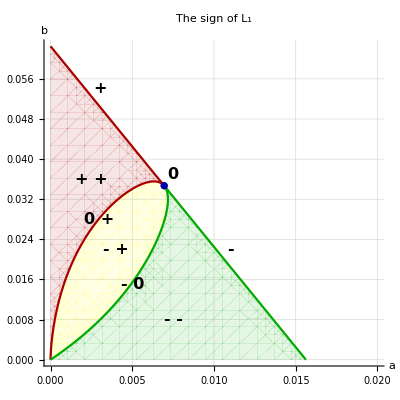

```mathematica
hopf=Solve[trJ==0&&a>0&&b>0&&t>0,a][[1]];
hopfbt=hopf[[1]][[2]][[2]];
asubst=Normal[hopf];
L1bt=Simplify[L1abt/.asubst];
bsubst=Normal[Solve[L1bt==0&&hopfbt,b][[1]]];
alim=1/50;
blim=1/16;
amax=1/64;
aspec=Simplify[a/.asubst/.bsubst/.{t->1/2}];
rgn1=Reduce[Exists[t,trJ==0&&t<1/2&&a>0&&b>0&&t>0&&L1abt>0]];
rgn2a=Reduce[Exists[t,trJ==0&&t>1/2&&a>0&&b>0&&t>0&&L1abt>0]];
rgn2b=Reduce[Exists[t,trJ==0&&t<1/2&&a>0&&b>0&&t>0&&L1abt<0]];
rgn2=rgn2a&&rgn2b;
rgn3=Reduce[Exists[t,trJ==0&&t>1/2&&a>0&&b>0&&t>0&&L1abt<0]];
rpl1=RegionPlot[rgn1,{a,0,alim},{b,0,blim},PlotStyle->{Darker[Red],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[a,Bold,16],Style[b,Bold,16]},Frame->None,Axes->True,PlotLabel->Style["The sign of L_1",Bold,16]];
rpl2=RegionPlot[rgn2,{a,0,alim},{b,0,blim},PlotStyle->{Yellow,Opacity[0.1]}, BoundaryStyle->None];
rpl3=RegionPlot[rgn3,{a,0,alim},{b,0,blim},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None];
pl1=Plot[1/16-4a,{a,0,aspec},PlotStyle->Darker[Red]];
pl2=Plot[1/16-4a,{a,aspec,amax},PlotStyle->Darker[Green]];
ppl1=ParametricPlot[{a/.asubst/.bsubst,b/.bsubst},{t,0,1/2},PlotStyle->Darker[Red]];
ppl2=ParametricPlot[{a/.asubst/.bsubst,b/.bsubst},{t,1/2,1},PlotStyle->Darker[Green]];
lpl=ListPlot[{{a/.asubst/.bsubst,b/.bsubst}/.{t->1/2}},PlotStyle->Darker[Blue]];
txt=Graphics[{Text[Style["+ +",Bold,16],{0.0025,0.036}],
Text[Style["0 +",Bold,16],{0.003,0.028}],
Text[Style["- +",Bold,16],{0.004,0.022}],
Text[Style["- 0",Bold,16],{0.005,0.015}],
Text[Style["- -",Bold,16],{0.0075,0.008}],
Text[Style["+",Bold,16],{0.003,0.054}],
Text[Style["0",Bold,16],{0.0075,0.037}],
Text[Style["-",Bold,16],{0.011,0.022}]}];
Show[rpl1,rpl2,rpl3,pl1,pl2,ppl1,ppl2,lpl,txt]
```

Now we find out the sign of  along the  curve in the -plane. This is performed by investigating its enumerator and denominator separately. Its denominator is positive, as it becomes apparent below.

```mathematica
L1abt=Simplify[Simplify[L1/.derivatives]/.ωsubst];
L2abt=Simplify[Simplify[ω^7 L2/.derivatives]/.ωsubst];
Reduce[a>0&&b>0&&t>0&&trJ==0&&Numerator[L1abt]==0&&Denominator[L2abt]>0,{b,a}]
Reduce[a>0&&b>0&&t>0&&trJ==0&&Numerator[L1abt]==0&&Numerator[L2abt]<0,{b,a}]
Reduce[a>0&&b>0&&t>0&&trJ==0&&Numerator[L1abt]==0&&Numerator[L2abt]==0,{b,a}]
Reduce[a>0&&b>0&&t>0&&trJ==0&&Numerator[L1abt]==0&&Numerator[L2abt]>0,{b,a}]
```

0<t<1&&b==(5 t^4-11 t^5-6 t^6-22 t^7-64 t^8-96 t^9-32 t^10-224 t^11)/(4 (1+4 t^2)^2 (1+t+4 t^3) (1+t+6 t^2+6 t^3))+1/4 √((16 t^4+164 t^6+244 t^7+491 t^8+2766 t^9+1175 t^10+10440 t^11+8304 t^12+12920 t^13+32668 t^14-3968 t^15+54976 t^16-17408 t^17+21888 t^18+36864 t^19-17408 t^20+26624 t^21+31744 t^22)/((1+4 t^2)^4 (1+t+4 t^3)^2 (1+t+6 t^2+6 t^3)^2))&&a==(b t^2-t^4+4 b t^4+t^5)/(-4 t^2-16 t^4)

0<t<Root0.958Root[«87»+40757086153685860352 #1^44+88384948532569178112 #1^45+130914664586978263040 #1^46+165123938700650086400 #1^47+184047218211160064000 #1^48+187614424167654359040 #1^49+178543424723937656832 #1^50+153799580135655997440 #1^51+126034079764159922176 #1^52+93932283525119082496 #1^53+63685563983551528960 #1^54+40740251334684442624 #1^55+22342982304054378496 #1^56+10843878361017614336 #1^57+4791222265649823744 #1^58+1440637472525516800 #1^59+307106310741032960 #1^60+56798880905297920 #1^61+11585828899782656 #1^62+3298672322281472 #1^63&,5]0.9582283555840174&&b==(5 t^4-11 t^5-6 t^6-22 t^7-64 t^8-96 t^9-32 t^10-224 t^11)/(4 (1+4 t^2)^2 (1+t+4 t^3) (1+t+6 t^2+6 t^3))+1/4 √((16 t^4+164 t^6+244 t^7+491 t^8+2766 t^9+1175 t^10+10440 t^11+8304 t^12+12920 t^13+32668 t^14-3968 t^15+54976 t^16-17408 t^17+21888 t^18+36864 t^19-17408 t^20+26624 t^21+31744 t^22)/((1+4 t^2)^4 (1+t+4 t^3)^2 (1+t+6 t^2+6 t^3)^2))&&a==(b t^2-t^4+4 b t^4+t^5)/(-4 t^2-16 t^4)

t==Root0.958Root[«87»+40757086153685860352 #1^44+88384948532569178112 #1^45+130914664586978263040 #1^46+165123938700650086400 #1^47+184047218211160064000 #1^48+187614424167654359040 #1^49+178543424723937656832 #1^50+153799580135655997440 #1^51+126034079764159922176 #1^52+93932283525119082496 #1^53+63685563983551528960 #1^54+40740251334684442624 #1^55+22342982304054378496 #1^56+10843878361017614336 #1^57+4791222265649823744 #1^58+1440637472525516800 #1^59+307106310741032960 #1^60+56798880905297920 #1^61+11585828899782656 #1^62+3298672322281472 #1^63&,5]0.9582283555840174&&b==(5 t^4-11 t^5-6 t^6-22 t^7-64 t^8-96 t^9-32 t^10-224 t^11)/(4 (1+4 t^2)^2 (1+t+4 t^3) (1+t+6 t^2+6 t^3))+1/4 √((16 t^4+164 t^6+244 t^7+491 t^8+2766 t^9+1175 t^10+10440 t^11+8304 t^12+12920 t^13+32668 t^14-3968 t^15+54976 t^16-17408 t^17+21888 t^18+36864 t^19-17408 t^20+26624 t^21+31744 t^22)/((1+4 t^2)^4 (1+t+4 t^3)^2 (1+t+6 t^2+6 t^3)^2))&&a==(-b+t^2-4 b t^2-t^3)/(4+16 t^2)

Root0.958Root[«87»+40757086153685860352 #1^44+88384948532569178112 #1^45+130914664586978263040 #1^46+165123938700650086400 #1^47+184047218211160064000 #1^48+187614424167654359040 #1^49+178543424723937656832 #1^50+153799580135655997440 #1^51+126034079764159922176 #1^52+93932283525119082496 #1^53+63685563983551528960 #1^54+40740251334684442624 #1^55+22342982304054378496 #1^56+10843878361017614336 #1^57+4791222265649823744 #1^58+1440637472525516800 #1^59+307106310741032960 #1^60+56798880905297920 #1^61+11585828899782656 #1^62+3298672322281472 #1^63&,5]0.9582283555840174<t<1&&b==(5 t^4-11 t^5-6 t^6-22 t^7-64 t^8-96 t^9-32 t^10-224 t^11)/(4 (1+4 t^2)^2 (1+t+4 t^3) (1+t+6 t^2+6 t^3))+1/4 √((16 t^4+164 t^6+244 t^7+491 t^8+2766 t^9+1175 t^10+10440 t^11+8304 t^12+12920 t^13+32668 t^14-3968 t^15+54976 t^16-17408 t^17+21888 t^18+36864 t^19-17408 t^20+26624 t^21+31744 t^22)/((1+4 t^2)^4 (1+t+4 t^3)^2 (1+t+6 t^2+6 t^3)^2))&&a==(b t^2-t^4+4 b t^4+t^5)/(-4 t^2-16 t^4)

Now we visualize the sign of .

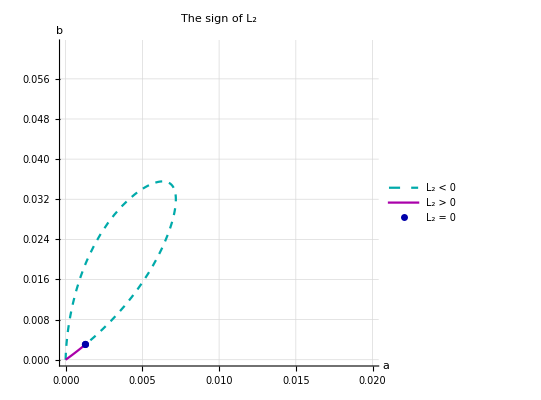

```mathematica
tspec=Root"0.958"Root[«87»+40757086153685860352 #1^44+88384948532569178112 #1^45+130914664586978263040 #1^46+165123938700650086400 #1^47+184047218211160064000 #1^48+187614424167654359040 #1^49+178543424723937656832 #1^50+153799580135655997440 #1^51+126034079764159922176 #1^52+93932283525119082496 #1^53+63685563983551528960 #1^54+40740251334684442624 #1^55+22342982304054378496 #1^56+10843878361017614336 #1^57+4791222265649823744 #1^58+1440637472525516800 #1^59+307106310741032960 #1^60+56798880905297920 #1^61+11585828899782656 #1^62+3298672322281472 #1^63&,5]0.9582283555840174;
rpl=RegionPlot[a>1,{a,0,alim},{b,0,blim},PlotStyle->{Darker[Green],Opacity[0.1]}, BoundaryStyle->None,GridLines->Automatic,AxesLabel->{Style[a,Bold,16],Style[b,Bold,16]},Frame->None,Axes->True,PlotLabel->Style["The sign of L_2",Bold,16]];
ppl1=ParametricPlot[{a/.asubst/.bsubst,b/.bsubst},{t,0,tspec},PlotStyle->{Darker[Cyan],Dashed},PlotRange->{{0,alim},{0,blim}},PlotLegends->Placed[{Style["L_2 < 0",Bold,16]},{0.77,0.81}]];
ppl2=ParametricPlot[{a/.asubst/.bsubst,b/.bsubst},{t,tspec,1},PlotStyle->Darker[Magenta],PlotRange->{{0,alim},{0,blim}},PlotLegends->Placed[{Style["L_2 > 0",Bold,16]},{0.77,0.6}]];
lpl=ListPlot[{{a/.asubst/.bsubst,b/.bsubst}/.{t->tspec}},PlotStyle->Darker[Blue],PlotLegends->Placed[{Style["L_2 = 0",Bold,16]},{0.78,0.705}]];
txt=Graphics[{Text[Style["-",Bold,16],{0.0025,0.036}],
Text[Style["0",Bold,16],{0.003,0.028}],
Text[Style["+",Bold,16],{0.004,0.022}]}];
Show[rpl,ppl1,ppl2,lpl]
```

Finally, we verify that  at the unique point  with .

```mathematica
derivatives=Simplify[GetDerivatives[fg,equilibrium,3],a>0&&b>0&&t>0];
L3bt=Simplify[Simplify[L3/.derivatives/.asubst]/.ωsubst/.asubst];
Print[" ",N[L3bt/.bsubst/.{t->tspec}]];
```

-3.37178